## Real gluon emission contribution to qq̄→(l̃)_i(l̃)_j

## Initialisation

Load FeynCalc and FeynArts. Furthermore, this notebook makes use of three packages found in the “include” folder.

```mathematica
description = "Leading order cross section of neutralino pair production at parton level.";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose = 0;

FCCheckVersion[9,3,1];
(FAPatch[PatchModelsOnly->True];)
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, check out the wiki or visit the forum.

Please check our FAQ for answers to some common FeynCalc questions and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Successfully patched FeynArts.

```mathematica
AppendTo[$Path,FileNameJoin[{NotebookDirectory[], "include"}]];
<< XSec`
<< TreeLevel`
<< CalcTools`
```

Index::shdw: Symbol Index appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

IndexDelta::shdw: Symbol IndexDelta appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

```mathematica
ResultsDir = FileNameJoin[{NotebookDirectory[], "results", "NLO"}];
```

## Generate Feynman diagrams and amplitudes

Some text

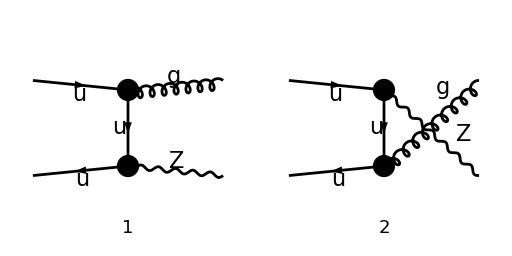

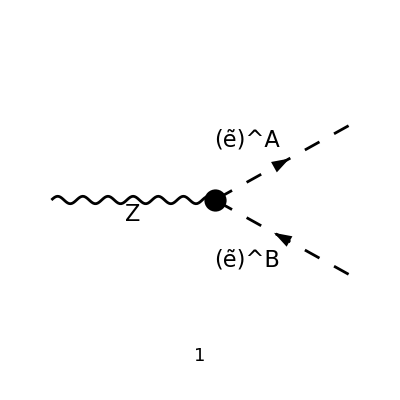

```mathematica
HDiagrams = InsertFields[
	CreateTopologies[0, 2 -> 2], 
	{F[3, {1}], -F[3, {1}]} -> {V[5], V[2]},
	InsertionLevel -> {Classes},
	Model -> MSSMQCD,
	Restrictions -> {NoLightFHCoupling, NoElectronHCoupling}(*,
	ExcludeParticles -> {F[11],F[12],S[1],S[2],S[3],S[4]}*)
];
LDiagrams = InsertFields[
	CreateTopologies[0, 1 -> 2], 
	{V[2]} -> {S[12, {A, 1}], -S[12, {B, 1}]},
	InsertionLevel -> {Classes},
	Model -> MSSMQCD(*,
	Restrictions -> {NoLightFHCoupling, NoElectronHCoupling},
	ExcludeParticles -> {F[11],F[12],S[1],S[2],S[3],S[4]}*)
];
Paint[HDiagrams, Numbering->Simple, ColumnsXRows -> {2, 1}, ImageSize->{512,256}];
Paint[LDiagrams, Numbering->Simple, ColumnsXRows -> {1, 1}, ImageSize->{512,256}];
```

```mathematica
Mhad[0] = FCFAConvert[
	CreateFeynAmp[HDiagrams], 
	IncomingMomenta -> {ki, kj},
	OutgoingMomenta -> {k, q},
	ChangeDimension -> D,
	UndoChiralSplittings -> True,
	List -> True,
	SMP -> True,
	DropSumOver -> True,
	LorentzIndexNames -> {ν,μ},
	FinalSubstitutions -> AmpSimplifyRules
] /. {IndexDelta -> FeynCalc`IndexDelta} /.
Pair[LorentzIndex[μ,_],Momentum[Polarization[q,_],_]] -> 1;

Mlep[0] = FCFAConvert[
	CreateFeynAmp[LDiagrams], 
	IncomingMomenta -> {q},
	OutgoingMomenta -> {pi, pj},
	ChangeDimension -> D,
	UndoChiralSplittings -> True,
	List -> True,
	SMP -> True,
	DropSumOver -> True,
	LorentzIndexNames -> {μ,ν}
] /. {IndexDelta -> FeynCalc`IndexDelta} /.
Pair[LorentzIndex[μ,_],Momentum[Polarization[q,_],_]] -> 1;
```

```mathematica
{Mhad[1], Mlep[1]} = ReplaceAll[#, ZSimplifyRules] &/@ {Mhad[0], Mlep[0]};
Mhad[2] = Mhad[1] // Total // DiracSimplify // ReplaceAll[#, Opp[i_,j_,L]* -> -Opp[i,j,R]]& // ReplaceRepeated[#, SuperChargeRules]&
Mlep[2] = Mlep[1] // Total // DiracSimplify // ReplaceAll[#, Opp[i_,j_,L]* -> -Opp[i,j,R]]& // ReplaceRepeated[#, SuperChargeRules]&
```

-(g_s g_W C_qqZ^L T_Col2Col1^Glu3 (φ(-k_j)).γ^μ.(γ·q).(γ·ε^*(k)).(γ̄)^7.(φ(k_i)))/(k_j-q)^2+(2 g_s g_W k_j^μ C_qqZ^L T_Col2Col1^Glu3 (φ(-k_j)).(γ·ε^*(k)).(γ̄)^7.(φ(k_i)))/(k_j-q)^2+(2 g_s g_W C_qqZ^L T_Col2Col1^Glu3 (k_j·ε^*(k)) (φ(-k_j)).γ^μ.(γ̄)^7.(φ(k_i)))/(k-k_j)^2-(g_s g_W C_qqZ^L T_Col2Col1^Glu3 (φ(-k_j)).(γ·ε^*(k)).(γ·k).γ^μ.(γ̄)^7.(φ(k_i)))/(k-k_j)^2-(g_s g_W C_qqZ^R T_Col2Col1^Glu3 (φ(-k_j)).γ^μ.(γ·q).(γ·ε^*(k)).(γ̄)^6.(φ(k_i)))/(k_j-q)^2+(2 g_s g_W k_j^μ C_qqZ^R T_Col2Col1^Glu3 (φ(-k_j)).(γ·ε^*(k)).(γ̄)^6.(φ(k_i)))/(k_j-q)^2+(2 g_s g_W C_qqZ^R T_Col2Col1^Glu3 (k_j·ε^*(k)) (φ(-k_j)).γ^μ.(γ̄)^6.(φ(k_i)))/(k-k_j)^2+-(g_s g_W C_qqZ^R T_Col2Col1^Glu3 (φ(-k_j)).(γ·ε^*(k)).(γ·k).γ^μ.(γ̄)^6.(φ(k_i)))/(k-k_j)^2

(e (p_j-p_i)^μ (USf(2,1)(A,1) Conjugate[(USf(2,1)(B,1))] (-3 C_qqZ^R (cos(θ_W))-1)-3 C_qqZ^R (cos(θ_W)) USf(2,1)(A,2) Conjugate[(USf(2,1)(B,2))]))/(2 (cos(θ_W)) (sin(θ_W)))

## Set scalar products

```mathematica
FCClearScalarProducts[];
SetMandelstamParameters[s, t, u, Q2];
SetMandelstam[s, t, u, ki, kj, -q, -k, 0, 0, Sqrt[Q2], 0];
ScalarProduct[pi, pj] = (Q2-MNeu[i]^2-MSf[B,2,1]^2)/2;
ScalarProduct[pi, q] = (Q2+MSf[A,2,1]^2-MSf[B,2,1]^2)/2;
ScalarProduct[pj, q] = (Q2-MSf[A,2,1]^2+MSf[B,2,1]^2)/2;
```

Replace propagators with Breit-Wigner approximations and simplify colour bit of the hadronic portion.

```mathematica
{Mhad[3], Mlep[3]} = (FeynAmpDenominatorExplicit /@ {Mhad[2], Mlep[2]}) /. {SMP["m_Z"]^2 -> DZ, MSf[args__]^2 -> DSf[args]};
Mhad[4] = SUNSimplify[Mhad[3]];
```

## Evaluate square amplitudes

### Slepton part

Square the amplitude and simplify sum over fermion chains

```mathematica
LepTensor[0] = (Mlep[3] ConjugateAmplitude[Mlep[3]/.μ->ν]) // FermionSpinSum // DiracSimplify
```

1/(4 (cos(θ_W))^2 (sin(θ_W))^2)e^2 (p_j-p_i)^μ (p_j-p_i)^ν (USf(2,1)(A,1) Conjugate[(USf(2,1)(B,1))] (-3 C_qqZ^R (cos(θ_W))-1)-3 C_qqZ^R (cos(θ_W)) USf(2,1)(A,2) Conjugate[(USf(2,1)(B,2))]) (USf(2,1)(B,1) Conjugate[(USf(2,1)(A,1))] (-3 C_qqZ^R (cos(θ_W))-1)-3 C_qqZ^R (cos(θ_W)) USf(2,1)(B,2) Conjugate[(USf(2,1)(A,2))])

```mathematica
Contract[Pair[LorentzIndex[μ], Momentum[q]] (LepTensor[0] // FCReplaceD[#, D->4]& // ChangeDimension[#, 4]&)] // Collect2[#, Pair[__], Factoring->Simplify]&
% /. B->A // Simplify
```

-1/(4 (cos(θ_W))^2 (sin(θ_W))^2)e^2 (OverBar[p_j]-OverBar[p_i])^ν (m_((q̃)_A)^2-m_((q̃)_B)^2) (USf(2,1)(A,1) Conjugate[(USf(2,1)(B,1))] (3 C_qqZ^R (cos(θ_W))+1)+3 C_qqZ^R (cos(θ_W)) USf(2,1)(A,2) Conjugate[(USf(2,1)(B,2))]) (USf(2,1)(B,1) Conjugate[(USf(2,1)(A,1))] (3 C_qqZ^R (cos(θ_W))+1)+3 C_qqZ^R (cos(θ_W)) USf(2,1)(B,2) Conjugate[(USf(2,1)(A,2))])

0

### Hadron part

Square the amplitude and simplify sum over fermion chains and polarisations of emitted gluon. Also disregard remaining Dirac traces with 4 γ-matrices and γ5.

```mathematica
HadTensor[0] = (Mhad[4] ConjugateAmplitude[Mhad[4]/.μ->ν]) // FermionSpinSum // DiracSimplify // DoPolarizationSums[#, k, 0]&;
HadTensor[1] = SelectFree2[HadTensor[0], DiracTrace];
```

Now we can make the result more presentable by calculating the colour factor and extracting a commong prefactor.

```mathematica
CommonPrefactor = CA CF SMP["g_s"]^2 SMP["g_W"]^2;
HadTensor[2] =  CommonPrefactor(HadTensor[1]/CommonPrefactor // SUNSimplify //
	Collect2[#, Pair[__], Factoring->Function[x, Simplify[TrickMandelstam[x, MandelstamParameters]]]]&)
```

C_A C_F g_s^2 g_W^2 (-(g^μν ((C_qqZ^L)^2+(C_qqZ^R)^2) ((D-2) t^2+2 (D-4) t u+(D-2) u^2+4 Q2^2-4 Q2 (t+u)))/(t u)+(2 (D-4) s k^ν q^μ ((C_qqZ^L)^2+(C_qqZ^R)^2))/(t u)+(2 (D-4) s k^μ q^ν ((C_qqZ^L)^2+(C_qqZ^R)^2))/(t u)-(2 (D-2) Q2 k^ν k_i^μ ((C_qqZ^L)^2+(C_qqZ^R)^2))/(t u)-(2 (D-2) Q2 k^μ k_i^ν ((C_qqZ^L)^2+(C_qqZ^R)^2))/(t u)+(2 k^ν k_j^μ (2 u-(D-4) s) ((C_qqZ^L)^2+(C_qqZ^R)^2))/(t u)+(2 k^μ k_j^ν (2 u-(D-4) s) ((C_qqZ^L)^2+(C_qqZ^R)^2))/(t u)+(2 q^μ k_j^ν ((C_qqZ^L)^2+(C_qqZ^R)^2) (D (t+u)-2 Q2+4 s))/(t u)+(2 q^ν k_j^μ ((C_qqZ^L)^2+(C_qqZ^R)^2) (D (t+u)-2 Q2+4 s))/(t u)-(2 k_i^ν k_j^μ ((C_qqZ^L)^2+(C_qqZ^R)^2) ((D-4) t+(D-2) u-2 Q2))/(t u)-(2 k_i^μ k_j^ν ((C_qqZ^L)^2+(C_qqZ^R)^2) ((D-4) t+(D-2) u-2 Q2))/(t u)-(4 k_j^μ k_j^ν ((C_qqZ^L)^2+(C_qqZ^R)^2) ((D-2) t+D u+2 s))/(t u)-(4 q^μ k_i^ν ((C_qqZ^L)^2+(C_qqZ^R)^2))/u-(4 q^ν k_i^μ ((C_qqZ^L)^2+(C_qqZ^R)^2))/u)

To get the final correct squared amplitude, we must contract the result with ϵ_μ(q)ϵ_ν*(q) to get the result and sum over the polarisations.

```mathematica
HadTensorContracted[0] = Pair[LorentzIndex[μ,D],Momentum[Polarization[q,-ⅈ],D]] Pair[LorentzIndex[ν,D],Momentum[Polarization[q,ⅈ],D]] HadTensor[2] // DoPolarizationSums[#, q]&;
HadTensorContracted[1] = HadTensorContracted[0] // TrickMandelstam[#, MandelstamParameters]& // Simplify
```

((D-2) C_A C_F g_s^2 g_W^2 ((C_qqZ^L)^2+(C_qqZ^R)^2) ((D-2) t^2+2 (D-4) t u+(D-2) u^2+4 Q2^2-4 Q2 (t+u)))/(t u)

## Phase Space Integration

Setting up some assumptions

```mathematica
$Assumptions = {
	s ∈ PositiveReals,
	Q2 ∈ PositiveReals,
	Mu2 ∈ PositiveReals,
	MSf[__] ∈ PositiveReals,
	z >= (MSf[A,2,1]+MSf[B,2,1])^2 / s,
	z <= 1,
	s >= (MSf[A,2,1]+MSf[B,2,1])^2,
	Q2 >= (MSf[A,2,1]+MSf[B,2,1])^2,
	Epsilon ∈ NegativeReals
};
```

### Slepton tensor

First the phase space factor.

```mathematica
PiLep[0] = p^(D-3)/(2^(D-1)Pi^((D-3)/2)Gamma[(D-1)/2]Sqrt[Q2]);
PiLep[1] = FCReplaceD[PiLep[0], D->4];
```

Knowing that N^μν = N_1 g^μν + N_2 (q^μ q^ν)/Q2 we can find the coefficients using the following contractions.

```mathematica
L1[0] = 1/(D-1)Contract[(Pair[LorentzIndex[μ,D], LorentzIndex[ν,D]] - (Pair[LorentzIndex[μ,D],Momentum[q,D]]Pair[LorentzIndex[ν,D],Momentum[q,D]])/Q2)LepTensor[0]] // Simplify
L2[0] = 1/(D-1)Contract[(-Pair[LorentzIndex[μ,D], LorentzIndex[ν,D]] + D(Pair[LorentzIndex[μ,D],Momentum[q,D]]Pair[LorentzIndex[ν,D],Momentum[q,D]])/Q2)LepTensor[0]] // Simplify
```

-1/(4 (D-1) Q2 (cos(θ_W))^2 (sin(θ_W))^2)e^2 (-2 m_((q̃)_A)^2 m_((q̃)_B)^2+m_((q̃)_A)^4-Q2 m_((q̃)_B)^2+m_((q̃)_B)^4-Q2 m_i^2+Q2^2-Q2 p_i^2-Q2 p_j^2) (USf(2,1)(A,1) Conjugate[(USf(2,1)(B,1))] (3 C_qqZ^R (cos(θ_W))+1)+3 C_qqZ^R (cos(θ_W)) USf(2,1)(A,2) Conjugate[(USf(2,1)(B,2))]) (USf(2,1)(B,1) Conjugate[(USf(2,1)(A,1))] (3 C_qqZ^R (cos(θ_W))+1)+3 C_qqZ^R (cos(θ_W)) USf(2,1)(B,2) Conjugate[(USf(2,1)(A,2))])

1/(4 (D-1) Q2 (cos(θ_W))^2 (sin(θ_W))^2)e^2 (-2 D m_((q̃)_A)^2 m_((q̃)_B)^2+D m_((q̃)_A)^4+D m_((q̃)_B)^4-Q2 m_((q̃)_B)^2-Q2 m_i^2+Q2^2-Q2 p_i^2-Q2 p_j^2) (USf(2,1)(A,1) Conjugate[(USf(2,1)(B,1))] (3 C_qqZ^R (cos(θ_W))+1)+3 C_qqZ^R (cos(θ_W)) USf(2,1)(A,2) Conjugate[(USf(2,1)(B,2))]) (USf(2,1)(B,1) Conjugate[(USf(2,1)(A,1))] (3 C_qqZ^R (cos(θ_W))+1)+3 C_qqZ^R (cos(θ_W)) USf(2,1)(B,2) Conjugate[(USf(2,1)(A,2))])

```mathematica
{N1[1], N2[1]} = Simplify /@ Expand /@ FCReplaceD[#, D->4] &/@ ChangeDimension[#, 4] &/@ {N1[0], N2[0]};
```

Setting up a function to get the neutralino tensor with given Lorentz index names.

```mathematica
LepTensor[mu_, nu_] := PiLep[1] (Pair[LorentzIndex[mu], LorentzIndex[nu]] L1[1] + (Pair[LorentzIndex[mu], Momentum[q]]Pair[LorentzIndex[nu], Momentum[q]])/Q2 L2[1])
```

### Hadronic tensor

```mathematica
PiHad = ((1-z)^(D-3)s^((D-4)/2))/(2^(D-1)Pi^((D-2)/2)Gamma[(D-2)/2])y^((D-4)/2)(1-y)^((D-4)/2);
```

```mathematica
MandelstamReplacements = {t -> -s(1-z)(1-y), u -> -s(1-z)y};
CommonPrefactor = (CA CF SMP["g_s"]^2SMP["g_W"]^2)/Pi;
```

```mathematica
Integrand = PiHad Mu2^((4-D)/2) HadTensorContracted[1] /. MandelstamReplacements // FCReplaceD[#, D->4-2Epsilon]&;
Result = Integrate[Integrand/CommonPrefactor, {y, 0, 1}];
% // Normal;
% /. (1-z)^(-2Epsilon-1) -> -1/(2Epsilon)DiracDelta[1-z] + PlusDistribution[1/(1-z)] - 2Epsilon PlusDistribution[Log[1-z]/(1-z)];
% / ((4Pi Mu2)/Q2)^Epsilon / (Gamma[1-Epsilon]/Gamma[1-2Epsilon]);
% // Expand // Series[#, {Epsilon, 0, 0}]& // Normal;
(*% // ReplaceAll[#, Epsilon -> 1/(SMP["Delta"]+EulerGamma-2Log[2]-Log[Pi])]&;*)
% /. Q2 -> z s;
(Coefficient[%, DiracDelta[1-z]] // ReplaceAll[#, z -> 1]&)DiracDelta[1-z] + SelectFree2[%//Expand, DiracDelta[1-z]];
% // Expand // ReplaceRepeated[SuperChargeRules];
% // Expand // Collect2[#, Epsilon, Factoring->Function[x, Collect2[x, {DiracDelta[_], PlusDistribution[_]}, Factoring->FullSimplify]]]&
```

(-(z-1 ((C_qqZ^L)^2+(C_qqZ^R)^2))-(z^2+1) (1/(1-z))_+ ((C_qqZ^L)^2+(C_qqZ^R)^2))/ε+(z-1 ((C_qqZ^L)^2+(C_qqZ^R)^2))/ε^2-(z^2+1) (1/(1-z))_+ (log(z)-1) ((C_qqZ^L)^2+(C_qqZ^R)^2)+2 (z^2+1) ((log(1-z))/(1-z))_+ ((C_qqZ^L)^2+(C_qqZ^R)^2)

```mathematica
% // Collect2[#, Epsilon, Factoring -> Isolate]&
```

(KK(1078))/ε+(KK(1079))/ε^2+KK(1075)

```mathematica
FRH[KK[1163]] /. FeynCalc`Collect`Private`unity -> 1 // Collect2[#, {DiracDelta[_], PlusDistribution[_]}, Factoring->FullSimplify]&
FRH[KK[1162]] /. FeynCalc`Collect`Private`unity -> 1 // Collect2[#, {DiracDelta[_], PlusDistribution[_]}, Factoring->FullSimplify]&
FRH[KK[1160]] /. FeynCalc`Collect`Private`unity -> 1 // Collect2[#, {DiracDelta[_], PlusDistribution[_]}, Factoring->FullSimplify]&
```

KK(1163)

KK(1162)

KK(1160)